```mathematica
z[t_]=E^(I*t)-.3 E^(I*3*t)+.2 E^(I*5*t)
```

ⅇ^(ⅈ t)-0.3 ⅇ^(3 ⅈ t)+0.2 ⅇ^(5 ⅈ t)

```mathematica
numbers={0,Pi/4,Pi/2,3Pi/4,Pi};
z[numbers]
```

{0.9,0.777817+0.353553 ⅈ,0.+1.5 ⅈ,-0.777817+0.353553 ⅈ,-0.9}

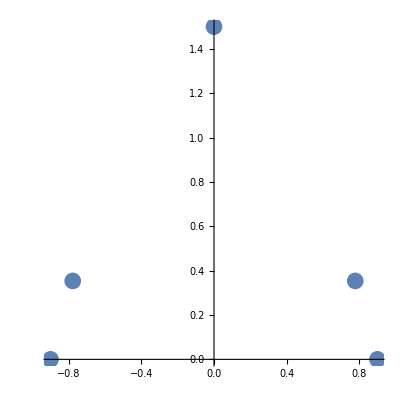

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@{0.8999999999999999,0.7778174593052023+0.3535533905932737 ⅈ,0.+1.5 ⅈ,-0.7778174593052022+0.35355339059327384 ⅈ,-0.8999999999999999},AspectRatio->1,PlotRange->All,PlotStyle->PointSize[.03]]
```

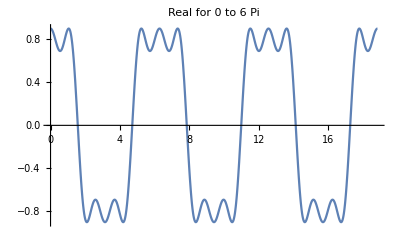

```mathematica
Plot[Re[z[t]],{t,0,6Pi},PlotLabel->"Real for 0 to 6 Pi"]
```

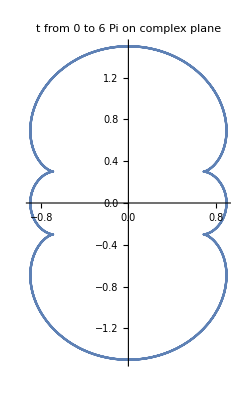

```mathematica
ParametricPlot[{Re[z[t]],Im[z[t]]},{t,0,6Pi}, PlotLabel->"t from 0 to 6 Pi on complex plane"]
```